```mathematica
ϵ=1;
Dp=0.4;
rc=1.5 Dp;
u=2ϵ(1/2 (Dp/r)^4-1)
v=Exp[Dp/(r-rc)+2]
Upatch=u v
```

2 (-1+0.0128/r^4)

ⅇ^(2+0.4/(-0.6+r))

2 ⅇ^(2+0.4/(-0.6+r)) (-1+0.0128/r^4)

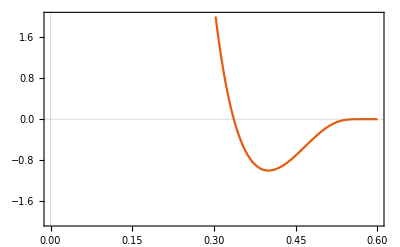

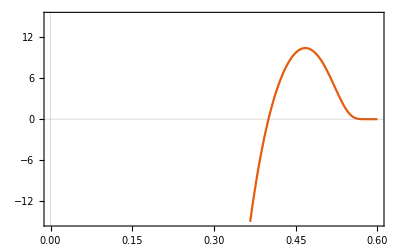

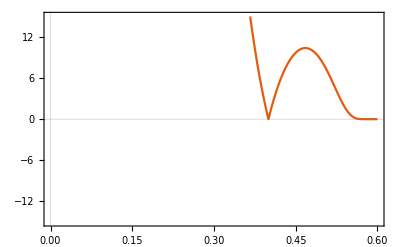

-Graphics-

-Graphics-

```mathematica
Plot[Upatch/.r->x,{x,0,rc},PlotRange->2,PlotTheme->"Scientific"]
Plot[D[Upatch,r]/.r->x,{x,0,rc},PlotRange->15,PlotTheme->"Scientific"]
Plot[Abs[D[Upatch,r]]/.r->x,{x,0,rc},PlotRange->15,PlotTheme->"Scientific"]
```

```mathematica
ClearAll[ϵ,Dp,rc]
u=2ϵ(1/2 (Dp/r)^4-1)
v=Exp[Dp/(r-rc)+2]
Upatch=u v

up=D[u,r]
vp=D[v,r]

dU=up v + u vp

D[Upatch,r]
D[Upatch,r]/.u->s
```

2 (-1+Dp^4/(2 r^4)) ϵ

ⅇ^(2+Dp/(r-rc))

2 ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ

-(4 Dp^4 ϵ)/r^5

-(Dp ⅇ^(2+Dp/(r-rc)))/(r-rc)^2

-(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5-(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

-(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5-(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

-(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5-(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

```mathematica
F=-dU
dF=D[F,r]

Module[{d=0.4},
Print[Solve[F==0,r]/.{Dp->d,rc->1.5 d}];
Print[Solve[dF==0,r,Reals]];
Print[Solve[dF==0,r,Reals]/.{Dp->d,rc->1.5 d}];
]
```

(4 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^5+(2 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^2

-(20 Dp^4 ⅇ^(2+Dp/(r-rc)) ϵ)/r^6-(2 Dp^2 ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^4-(4 Dp ⅇ^(2+Dp/(r-rc)) (-1+Dp^4/(2 r^4)) ϵ)/(r-rc)^3-(8 Dp^5 ⅇ^(2+Dp/(r-rc)) ϵ)/(r^5 (r-rc)^2)

{{r→0.4},{r→-0.490556-0.508787 ⅈ},{r→-0.490556+0.508787 ⅈ},{r→0.290556-0.382366 ⅈ},{r→0.290556+0.382366 ⅈ}}

{{r→ConditionalExpression[Root[-20 Dp^3 rc^4+(-8 Dp^4 rc^2+80 Dp^3 rc^3) #1+(-Dp^5+18 Dp^4 rc-120 Dp^3 rc^2) #1^2+(-10 Dp^4+80 Dp^3 rc) #1^3-20 Dp^3 #1^4+(2 Dp-4 rc) #1^6+4 #1^7&,1], ]},{r→ConditionalExpression[Root[-20 Dp^3 rc^4+(-8 Dp^4 rc^2+80 Dp^3 rc^3) #1+(-Dp^5+18 Dp^4 rc-120 Dp^3 rc^2) #1^2+(-10 Dp^4+80 Dp^3 rc) #1^3-20 Dp^3 #1^4+(2 Dp-4 rc) #1^6+4 #1^7&,2], ]},{r→ConditionalExpression[Root[-20 Dp^3 rc^4+(-8 Dp^4 rc^2+80 Dp^3 rc^3) #1+(-Dp^5+18 Dp^4 rc-120 Dp^3 rc^2) #1^2+(-10 Dp^4+80 Dp^3 rc) #1^3-20 Dp^3 #1^4+(2 Dp-4 rc) #1^6+4 #1^7&,3], ]}}

{{r→0.467624},{r→Undefined},{r→Undefined}}

```mathematica
dF1=dF/.{Dp->0.4,rc->1.4*0.4,ϵ->1}
```

-(0.32 ⅇ^(2+0.4/(-0.56+r)) (-1+0.0128/r^4))/(-0.56+r)^4-(1.6 ⅇ^(2+0.4/(-0.56+r)) (-1+0.0128/r^4))/(-0.56+r)^3-(0.512 ⅇ^(2+0.4/(-0.56+r)))/r^6-(0.08192 ⅇ^(2+0.4/(-0.56+r)))/((-0.56+r)^2 r^5)

```mathematica
Solve[dF1==0,r]
```

{{r→-0.728957-0.694742 ⅈ},{r→-0.728957+0.694742 ⅈ},{r→0.294436-0.541238 ⅈ},{r→0.294436+0.541238 ⅈ},{r→0.394294-0.173591 ⅈ},{r→0.394294+0.173591 ⅈ},{r→0.440454}}

```mathematica
rcF=r/.Solve[dF1==0,r]
```

{-0.728957-0.694742 ⅈ,-0.728957+0.694742 ⅈ,0.294436-0.541238 ⅈ,0.294436+0.541238 ⅈ,0.394294-0.173591 ⅈ,0.394294+0.173591 ⅈ,0.440454}

```mathematica
F/.{Dp->0.4,rc->1.4*0.4,ϵ->1}
reval=F/.{r->rcF[[7]],Dp->0.4,rc->1.4*0.4,ϵ->1}
```

(0.8 ⅇ^(2+0.4/(-0.56+r)) (-1+0.0128/r^4))/(-0.56+r)^2+(0.1024 ⅇ^(2+0.4/(-0.56+r)))/r^5

-8.00697

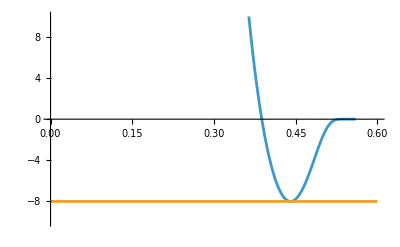

```mathematica
Plot[{(0.8 ⅇ^(2+0.4/(-0.5599999999999999+r)) (-1+0.012800000000000006/r^4))/(-0.5599999999999999+r)^2+(0.10240000000000005 ⅇ^(2+0.4/(-0.5599999999999999+r)))/r^5,reval},{r,0,1.5 * 0.4},PlotRange->10]
```

```mathematica
rcF[[7]]
```

0.440454

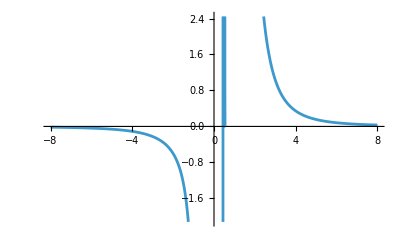

```mathematica
Plot[dF1,{r,-8,8}]
```

```mathematica
up
u
```

-(4 Dp^4 ϵ)/r^5

2 (-1+Dp^4/(2 r^4)) ϵ

```mathematica
Simplify[2 (-1+Dp^4/(2 r^4)) ϵ]
```

(-2+Dp^4/r^4) ϵ

```mathematica
Expand[(-2+Dp^4/r^4) ϵ]
```

-2 ϵ+(Dp^4 ϵ)/r^4

```mathematica
dif=up-u
dif2=u-up

FullSimplify[dif2]
(up+dif2)-u //Simplify
u//Simplify
```

-2 (-1+Dp^4/(2 r^4)) ϵ-(4 Dp^4 ϵ)/r^5

2 (-1+Dp^4/(2 r^4)) ϵ+(4 Dp^4 ϵ)/r^5

(-2+(Dp^4 (4+r))/r^5) ϵ

0

(-2+Dp^4/r^4) ϵ

```mathematica
Simplify[2 (-1+Dp^4/(2 r^4)) ϵ+(4 Dp^4 ϵ)/r^5]
```

(-2+(Dp^4 (4+r))/r^5) ϵ

```mathematica
ExpandAll[-2 (-1+Dp^4/(2 r^4)) ϵ-(4 Dp^4 ϵ)/r^5]
```

2 ϵ-(4 Dp^4 ϵ)/r^5-(Dp^4 ϵ)/r^4

```mathematica
Simplify[2 ϵ-(4 Dp^4 ϵ)/r^5-(Dp^4 ϵ)/r^4]
```

(2-(Dp^4 (4+r))/r^5) ϵ

```mathematica
Expand[(-2+Dp^4/r^4) ϵ]
```

-2 ϵ+(Dp^4 ϵ)/r^4

```mathematica
Root
```

```mathematica
Solve[1/x^4 ((x-1.5 d)^2/x-d/4)+1/(2 d^3)==0,x,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→Root[9. d^5-13. d^4 #1+4. d^3 #1^2+2. #1^5&,1]}}

```mathematica
x/.{{x->Root[9. d^5-13. d^4 #1+4. d^3 #1^2+2. #1^5&,1]}}
```

{Root[9. d^5-13. d^4 #1+4. d^3 #1^2+2. #1^5&,1]}

```mathematica
d=0.4
Root[1/x^4 ((x-1.5 d)^2/x-d/4)+1/(2 d^3),1]
```

0.4

-0.754489

```mathematica
Simplify[1/(2 d^3)+(-d/4+(-c+x)^2/x)/x^4]
```

1/(2 d^3)+(c-x)^2/x^5-d/(4 x^4)

```mathematica
ResourceFunction["Intercepts"][1/(2 d^3)+(c-x)^2/x^5-d/(4 x^4),{x,y}]
```

[1/(2 d^3)+(c-x)^2/x^5-d/(4 x^4),{x,y}]

```mathematica
Information[ResourceFunction["Intercepts"]]
```

Resource Function

```mathematica
Manipulate[Plot[1/(2 d^3)+(-d/4+(-c+x)^2/x)/x^4,{x,-8,8}],{c,-8,8},{d,-2,2}]
```

```mathematica
0.4 1.8
```

0.72

1/x^4 ((x-1.5 d)^2/x - d/4) + 1/(2 d^3)=0

WolframAlphaQueryResults